# MS-C2105: Introduction to Optimization // Week 5

Harri Hakula, 2022

## Gradient Method

```mathematica
GeneratePath[A_,b_,x0_]:=With[{tol=0.01},
Module[{g,path,mu,x},
x=x0;
path={x};
g=A.x-b;
While[Norm[g]>tol,
mu=(g.g)/(g.A.g);
x=x-mu g;
g=A.x-b;
AppendTo[path,x];
];
path
]
]
```

## First Example

```mathematica
A={{2,-1},{-1,2}}; MatrixForm[A]
```

(2 | -1
-1 | 2)

```mathematica
b=A.{1,1}; MatrixForm[b]
```

(1
1)

```mathematica
x=.;Expand[(1/2){x,y}.A.{x,y}-{x,y}.b]
```

-x+x^2-y-x y+y^2

Solve  is equivalent to Minimize  f(x,y) =

## Let us take a closer look

```mathematica
Plot3D[(1/2){x,y}.A.{x,y}-{x,y}.b,{x,-1,3},{y,-1,3}]
```

-Graphics3D-

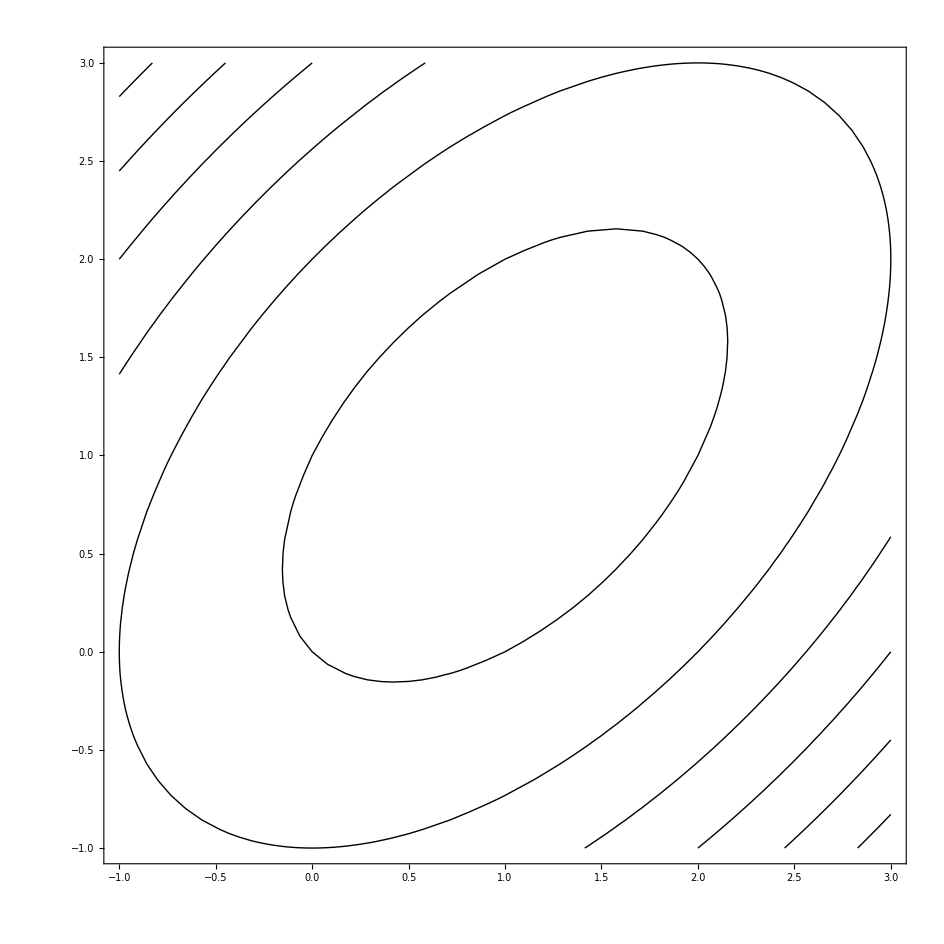

```mathematica
base0=ContourPlot[(1/2){x,y}.A.{x,y}-{x,y}.b,{x,-1,3},{y,-1,3},ContourShading->None]
```

## First Run

Initial guess is .

```mathematica
x={2,-1};
```

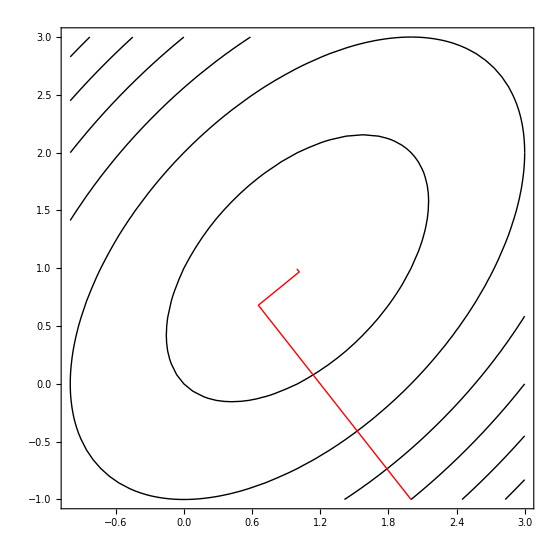

```mathematica
path=GeneratePath[A,b,x];
Show[base0,Graphics[{Red,Line[path]}]]
```

## Animation

```mathematica
x={2,-1};path=GeneratePath[A,b,x];Manipulate[Show[base0,Graphics[{Red,Line[path[[1;;u]]]}],ImageSize->Full],{u,2,Length[path],1},ContentSize->{460, 460}]
```

## Another

Initial guess is .

```mathematica
x={0,-1};
```

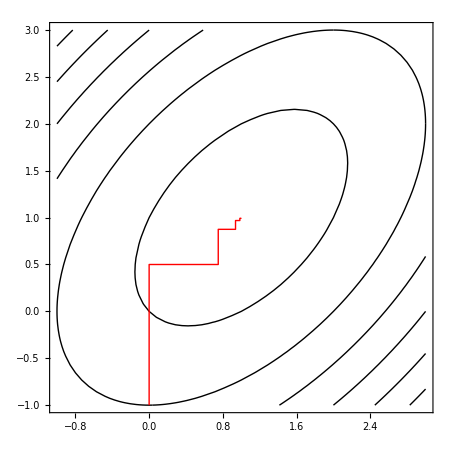

```mathematica
path=GeneratePath[A,b,x];
Show[base0,Graphics[{Red,Line[path]}]]
```

## Animation

```mathematica
x={0,-1};path=GeneratePath[A,b,x];Manipulate[Show[base0,Graphics[{Red,Line[path[[1;;u]]]}],ImageSize->Full],{u,2,Length[path],1},ContentSize->{460, 460}]
```

## What is the worst that can happen?

```mathematica
A={{2,-1},{-4,10}}; MatrixForm[A]
```

(2 | -1
-4 | 10)

```mathematica
b=A.{1,1}; MatrixForm[b]
```

(1
6)

```mathematica
x=.;Expand[(1/2){x,y}.A.{x,y}-{x,y}.b]
```

-x+x^2-6 y-(5 x y)/2+5 y^2

Solve  is equivalent to Minimize  f(x,y) =

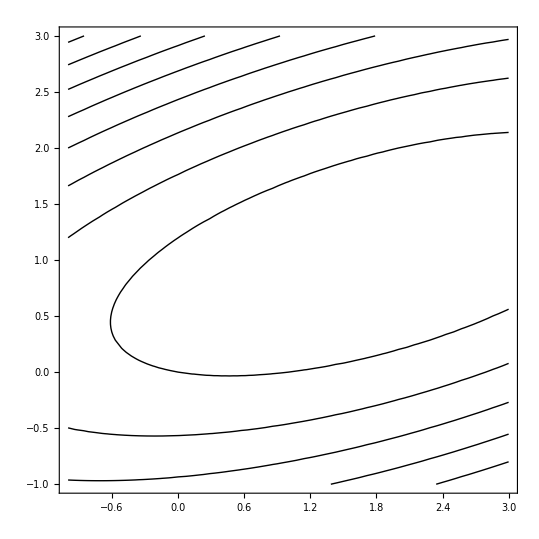

```mathematica
base=ContourPlot[(1/2){x,y}.A.{x,y}-{x,y}.b,{x,-1,3},{y,-1,3},ContourShading->None]
```

## Bad guess?

Initial guess is .

```mathematica
x={-1,-1/2};
```

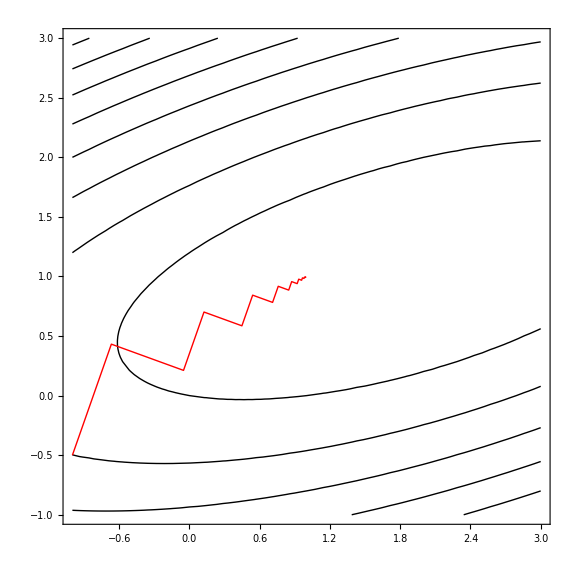

```mathematica
path=GeneratePath[A,b,x];
Show[base,Graphics[{Red,Line[path]}]]
```

```mathematica
Manipulate[Show[base,Graphics[{Red,Line[path[[1;;u]]]}],ImageSize->Full],{u,2,Length[path],1},ContentSize->{460, 460}]
```